## Black Hole Mirages: electron lensing and Berry curvature effects in inhomogeneously tilted Weyl semimetals

Andreas Haller^*, Suraj Hegde, Chen Xu, Christophe De Beule, Thomas L. Schmidt, Tobias Meng
* andreas.haller@uni.lu

### Auxiliary Functions and Modules

#### SEOM Solutions

```mathematica
(* some auxiliary functions *)
Clear[norm,hat,ρ,ρs,v,α,r]
norm[v_]:=√(v.v);(* convenient norm *)
hat[v_]:=v/norm[v];(* unit vector *)
ρ[v_]:={v[[1]],v[[2]],0v[[3]]};(* sph.<->cyl. : 0v[[3]] <-> v[[3]]*)
ρs[r_,α_]:=r(1+α)^(1/(2 α));
Clear[L,spin,J, xv,kv,χ]
L[xv_,kv_]:=xv×kv; (* angular momentum *)
spin[χ_,kv_]:=χ/2 hat[kv];
J[χ_,xv_,kv_]:=L[xv,kv]+spin[χ,kv]; (* total angular momentum *)
Clear[u,r,vF,rt,r,α,v]
u[α_,vF_,rt_,r_]:=-vF(rt/r)^α;(* scalar part of the tilt *)
uv[α_,vF_,rt_,v_]:=u[α,vF,rt,norm[ρ[v]]]*hat[ρ[v]]; (* tilt *)
Ω[χ_,v_]:=χ/2 v/norm[v]^3;(* Berry curvature *)
ϵ[α_,vF_,rt_,xs_,ks_]:=uv[α,vF,rt,ρ[xs]].ks+vF*norm[ks];(* energy dispersion *)

(* the main module for solving the SEOM *)
Clear[solveSEOM,x0,k0,vF,rt,α,χ,ti,tf,t]
solveSEOM[s_,x0_,k0_,vF_,rt_,α_,χ_,ti_:-20,tf_:20,pΩ_:+1.0]:=Module[
(* define variables in module scope *)
{xv,kv, r,x,y,z,kx,ky,kz,eq1,eq2,eq3,eq4, problem, solution,xvs,kvs,tstop,return,t}
,
(* module body *)
xv[t_]:={x[t],y[t],z[t]};
kv[t_]:={kx[t],ky[t],kz[t]};

eq1[t_]:=(xv'[t]==+D[ϵ[α,vF,rt,xv[t],kv[t]],{kv[t],1}]+pΩ*kv'[t]×Ω[χ,kv[t]]);
eq2[t_]:=(kv'[t]==-D[ϵ[α,vF,rt,xv[t],kv[t]],{xv[t],1}]);

(* set initial conditions *)
eq4:=(kv[0]==k0);
eq3:=(xv[0]==x0);

(* combine the eq's defined above with a stopping criterion *)
tstop=∞;
problem[t_]:=Join[Flatten[Table[#[[1,j]]==#[[2,j]],{j,Length[#[[1]]]}]&/@{eq1[t],eq2[t],eq3,eq4}],{WhenEvent[√(x'[t]^2+y'[t]^2+z'[t]^2)≥5,tstop=t;"StopIntegration"]}];
(* numerically solve the coupled differential equation *)
solution[t_]=First[NDSolve[problem[t],Flatten[{xv[t],kv[t]}],{t,ti,tf}]];

(* this might not catch all errors, but it'll do for the examples in this notebook *)
tstop=Min[{tstop,tf}];
If[tstop<tf,Print["WATCHOUT: tstop="<>ToString[tstop]]];

return[t_]:={xv[t]/.solution[t], kv[t]/.solution[t]};

(* return *)
return[s]
];
```

```mathematica
(* random test case *)
Clear[x0,k0,s,t,vF,α,χ,ti,tf,ρt]
{x0,k0}:={{RandomReal[{-5,5}],0,0},{0,RandomReal[{-1,1}],0}};
```

```mathematica
solveSEOM[s,x0,k0,vF=1,ρt=1,α=1/2,χ=+1]//AbsoluteTiming
```

WATCHOUT: tstop=1.14912

{0.012901,{{InterpolatingFunction[…][s],InterpolatingFunction[…][s],InterpolatingFunction[…][s]},{InterpolatingFunction[…][s],InterpolatingFunction[…][s],InterpolatingFunction[…][s]}}}

#### Plotting

```mathematica
<<MaTeX`
SetOptions[Plot,PlotTheme->"Scientific",PlotRange->All];
SetOptions[ParametricPlot,PlotTheme->"Scientific",PlotRange->All];
SetOptions[LogLinearPlot,PlotTheme->"Scientific",PlotRange->All];
SetOptions[LogLogPlot,PlotTheme->"Scientific",PlotRange->All];
SetOptions[ListPlot,PlotTheme->"Scientific",PlotRange->All];
SetOptions[ListLogLinearPlot,PlotTheme->"Scientific",PlotRange->All];
SetOptions[ListLogLogPlot,PlotTheme->"Scientific",PlotRange->All];

Clear[makePlots]
makePlots[xk_,ρt_,α_,χ_,ti_:-20,tf_:20,print_:True]:=Module[{allPlots,photonSphere,photonCylinder,inset,trajXV,trajDTXV,trajKV,angMom,sPlot,totAngMom,dtTotAngMom,dtJLSZ,t,tpr},
photonSphere=Graphics3D[Sphere[{0,0,0},#]&/@{ρt,ρt(1+α)^(1/(2α))}];
photonCylinder=Graphics3D[Cylinder[{0,0,xk[#][[1]][[3]]}&/@{ti,tf},#]&/@{1,(1+α)^(1/(2α))}];

If[ρ[{0,0,1}][[3]]==1,inset=photonSphere,inset=photonCylinder];

trajXV=Show[ParametricPlot3D[Evaluate[xk[t][[1]]],{t,ti,tf},AxesLabel->{"x","y","z"},PlotRange->Full],Graphics3D[Arrow[Tube[Table[xk[t][[1]],{t,{(tf+ti)/2,(tf+ti)/2+0.001*(tf-ti)}}]]]],inset,ViewPoint->Top,PlotLabel->MaTeX["\\text{spatial trajectory}"]];
trajDTXV=Show[ParametricPlot3D[Evaluate[xk'[t][[1]]],{t,ti,tf},PlotRange->Full,AxesLabel->{"x","y","z"}],Graphics3D[Arrow[Tube[Table[xk'[t][[1]],{t,{(tf+ti)/2,(tf+ti)/2+0.001*(tf-ti)}}]]]],ViewPoint->Top,PlotLabel->MaTeX["\\text{velocity trajectory}"]];
trajKV=Show[ParametricPlot3D[Evaluate[xk[t][[2]]],{t,ti,tf},PlotRange->Full,AxesLabel->{"x","y","z"}],Graphics3D[Arrow[Tube[Table[xk[t][[2]],{t,{(tf+ti)/2,(tf+ti)/2+0.001*(tf-ti)}}]]]],ViewPoint->Top,PlotLabel->MaTeX["\\text{momentum trajectory}"]];
angMom=Plot[Evaluate[L[Sequence@@xk[t]]],{t,ti,tf},PlotRange->All,PlotLabel->MaTeX["\\text{Angular moment}"],PlotLegends->MaTeX[{"L_x","L_y","L_z"}],FrameLabel->MaTeX[{"\\text{time (a.u.)}"}]];
sPlot=Plot[Evaluate[spin[χ,xk[t][[2]]]],{t,ti,tf},PlotRange->All,PlotLabel->MaTeX["\\text{Spin}"],PlotLegends->MaTeX[{"s_x","s_y","s_z"}],FrameLabel->MaTeX[{"\\text{time (a.u.)}"}]];
totAngMom=Plot[Evaluate[J[χ,Sequence@@xk[t]]],{t,ti,tf},PlotRange->All,PlotLabel->MaTeX["\\text{Total angular moment}"],PlotLegends->MaTeX[{"J_x","J_y","J_z"}],FrameLabel->MaTeX[{"\\text{time (a.u.)}"}]];
dtTotAngMom=Plot[Evaluate[D[J[χ,Sequence@@xk[t]],tpr]/.{tpr->t}],{t,ti,tf},PlotRange->All,PlotLabel->MaTeX["\\text{Time derivative of total angular moment}"],PlotLegends->MaTeX[{"\\dot J_x","\\dot J_y","\\dot J_z"}],FrameLabel->MaTeX[{"\\text{time (a.u.)}"}]];
dtJLSZ=Plot[Evaluate[{D[spin[χ,xk[tpr][[2]]],tpr][[3]], D[L[Sequence@@xk[tpr]],tpr][[3]],D[J[χ,Sequence@@xk[t]],tpr][[3]]}/.{tpr->t}],{t,ti,tf},PlotRange->All,PlotLabel->MaTeX["\\text{Time derivative of z-components of $\\bf J$, $\\bf L$ and $\\bf S$}"],PlotLegends->MaTeX[{"\\dot s_z","\\dot L_z","\\dot J_z"}],FrameLabel->MaTeX[{"\\text{time (a.u.)}"}]];
allPlots={trajXV,trajDTXV,trajKV,angMom,sPlot,totAngMom,dtTotAngMom,dtJLSZ};
If[print,Print[#]&/@allPlots];
allPlots
];
```

```mathematica
(* random test case *)
Clear[x0,k0,s,t,vF,α,χ,ti,tf,ρt]
{x0,k0}:={{8+RandomReal[{-5,5}],0,0},{0,RandomReal[{-1,1}],0}};
```

```mathematica
Clear[fun,s]
fun[s_]=solveSEOM[s,x0,k0,vF=1,ρt=1,α=1/2,χ=+1];//AbsoluteTiming
```

{0.005899,Null}

-Graphics3D-

-Graphics3D-

-Graphics3D-

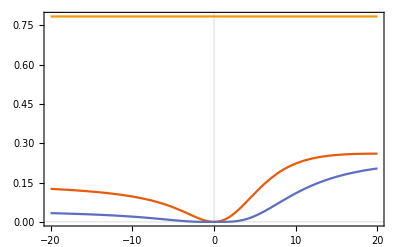

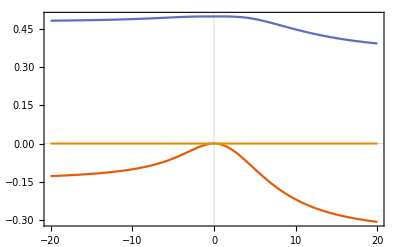

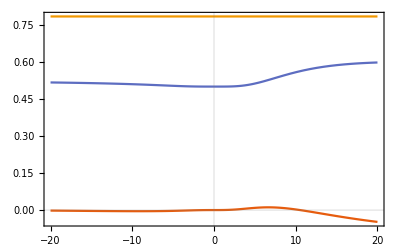

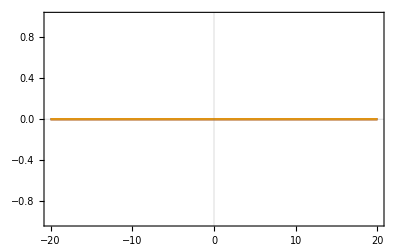

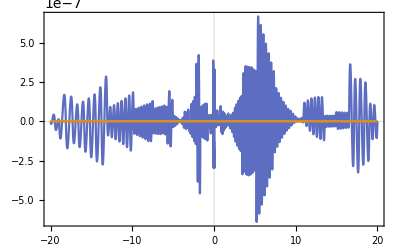

```mathematica
makePlots[fun,ρt,α,χ];
```

```mathematica
Clear[makePlots2D,ρt,α,χ,xk,ti,tf,ax1,ax2,print,t]
makePlots2D[xk_,ρt_,α_,χ_,ti_:-20,tf_:20,ax1_:1,ax2_:2,print_:True]:=Module[{allPlots,photonSphere,photonCylinder,inset,trajXV,trajDTXV,trajKV,angMom,sPlot,totAngMom,dtTotAngMom,dtJLSZ,t,tpr},
inset=If[{ax1,ax2}=={1,2}||{ax1,ax2}=={2,1},Graphics[{Opacity[0.3],Disk[{0,0},#]}&/@{ρt,ρt(1+α)^(1/(2α))}],{}];
trajXV=Show[ParametricPlot[Evaluate[xk[t][[1]][[{ax1,ax2}]]],{t,ti,tf},FrameLabel->{"x","y","z"}[[{ax1,ax2}]]],Graphics[Arrow[Line[Table[xk[t][[1]][[{ax1,ax2}]],{t,{(tf+ti)/2,(tf+ti)/2+0.001*(tf-ti)}}]]]],inset,ViewPoint->Top,PlotLabel->MaTeX["\\text{spatial trajectory}"]];
trajDTXV=Show[ParametricPlot[Evaluate[xk'[t][[1]][[{ax1,ax2}]]],{t,ti,tf},FrameLabel->{"x","y","z"}[[{ax1,ax2}]]],Graphics[Arrow[Line[Table[xk'[t][[1]][[{ax1,ax2}]],{t,{(tf+ti)/2,(tf+ti)/2+0.001*(tf-ti)}}]]]],ViewPoint->Top,PlotLabel->MaTeX["\\text{velocity trajectory}"]];
trajKV=Show[ParametricPlot[Evaluate[xk[t][[2]][[{ax1,ax2}]]],{t,ti,tf},FrameLabel->{"x","y","z"}[[{ax1,ax2}]]],Graphics[Arrow[Line[Table[xk[t][[2]][[{ax1,ax2}]],{t,{(tf+ti)/2,(tf+ti)/2+0.001*(tf-ti)}}]]]],ViewPoint->Top,PlotLabel->MaTeX["\\text{momentum trajectory}"]];
angMom=Plot[Evaluate[L[Sequence@@xk[t]]],{t,ti,tf},PlotRange->All,PlotLabel->MaTeX["\\text{Angular moment}"],PlotLegends->MaTeX[{"L_x","L_y","L_z"}],FrameLabel->MaTeX[{"\\text{time (a.u.)}"}]];
sPlot=Plot[Evaluate[spin[χ,xk[t][[2]]]],{t,ti,tf},PlotRange->All,PlotLabel->MaTeX["\\text{Spin}"],PlotLegends->MaTeX[{"s_x","s_y","s_z"}],FrameLabel->MaTeX[{"\\text{time (a.u.)}"}]];
totAngMom=Plot[Evaluate[J[χ,Sequence@@xk[t]]],{t,ti,tf},PlotRange->All,PlotLabel->MaTeX["\\text{Total angular moment}"],PlotLegends->MaTeX[{"J_x","J_y","J_z"}],FrameLabel->MaTeX[{"\\text{time (a.u.)}"}]];
dtTotAngMom=Plot[Evaluate[D[J[χ,Sequence@@xk[tpr]],tpr]/.{tpr->t}],{t,ti,tf},PlotRange->All,PlotLabel->MaTeX["\\text{Time derivative of total angular moment}"],PlotLegends->MaTeX[{"\\dot J_x","\\dot J_y","\\dot J_z"}],FrameLabel->MaTeX[{"\\text{time (a.u.)}"}]];
dtJLSZ=Plot[Evaluate[{D[spin[χ,xk[tpr][[2]]],tpr][[3]], D[L[Sequence@@xk[tpr]],tpr][[3]],D[J[χ,Sequence@@xk[t]],tpr][[3]]}/.{tpr->t}],{t,ti,tf},PlotRange->All,PlotLabel->MaTeX["\\text{Time derivative of z-components of $\\bf J$, $\\bf L$ and $\\bf S$}"],PlotLegends->MaTeX[{"\\dot s_z","\\dot L_z","\\dot J_z"}],FrameLabel->MaTeX[{"\\text{time (a.u.)}"}]];
allPlots={trajXV,trajDTXV,trajKV,angMom,sPlot,totAngMom,dtTotAngMom,dtJLSZ};
If[print,Print[#]&/@allPlots];
allPlots
];
```

```mathematica
(* test case *)
Clear[x0,k0,s,t,vF,α,χ,ti,tf,ρt]
{x0,k0}={{1.67,0,0},{1,1,0}};
```

{0.006182,Null}

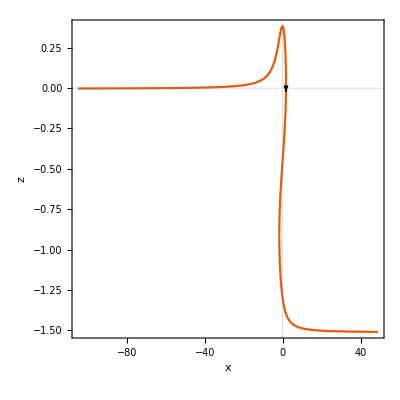

```mathematica
Clear[fun,s]
fun[s_]=solveSEOM[s,x0,k0,vF=1,ρt=1,α=1/2,χ=+1,ti=-100,tf=100];//AbsoluteTiming
plots=makePlots2D[fun,ρt,α,χ,ti,tf,1,3,False];
(*plots=makePlots[fun,ρt,α,χ,ti,tf];*)
Show[plots[[1]],AspectRatio->1,ImageSize->400]
```

#### Lensing Angle

```mathematica
Clear[lensingAngle,x0,k0,fun,vF,rt,ρt,α,χ,nti,ntf,ti,tf,t]
lensingAngle[x0_,k0_,vF_,rt_,α_,χ_,nti_,ntf_,check_:True]:=Module[{t,b,fun,ti,tf,rp,plots,closestApproach,tp,ϵp,Lzp,ϵdiff,Lzdiff,ϵts,Lzts,xvts,lensingAngleNumeric,lensingAngleAnalytic1,lensingAngleAnalytic2,lensingPlot},
ti=nti;tf=ntf;
(* obtain solution with initial conditions x0, k0 *)
fun[b_]:=Evaluate@solveSEOM[b,x0,k0,vF,rt,α,χ,ti,tf];
(* extract periapsis *)
closestApproach[b_]=NMinimize[norm[fun[b][[1]][[;;2]]],b];
rp=First[closestApproach[t]];
(*Print[ToString[StringForm["Periapsis: `1`",ρp]]]*)
tp=t/.closestApproach[t][[2]];

ϵts=ϵ[α,vF,rt,Sequence@@fun[#]]&/@{ti,tf};
ϵdiff=Subtract@@ϵts;
Lzts=L[Sequence@@fun[#]][[3]]&/@{ti,tf};
Lzdiff=Subtract@@Lzts;
If[check,
If[Abs[ϵdiff/ϵts[[1]]]>10^-4,Print["Check conserved quantities."]];
If[Abs[Lzdiff/Lzts[[1]]]>10^-4,Print["Check conserved quantities."]];
];
(* extract initial/final direction vector *)
xvts=Normalize[fun'[#][[1]]]&/@{ti,tf};
lensingAngleNumeric=VectorAngle@@xvts;
(* compare to analytics *)
lensingAngleAnalytic1=NIntegrate[2(vF/(√(1/rp^2(vF^2-u[α,vF,rt,rp]^2)r^4-r^2(vF^2-u[α,vF,rt,r]^2)))),{r,rp,∞}]-π;
lensingAngleAnalytic2=u[α,vF,rt,rp]^2/vF^2 NIntegrate[(r^2-rp^2 (rp/r)^(2α))/(r^2-rp^2)rp/(r √(r^2-rp^2)),{r,rp,∞}];
(* result *)
{rp,lensingAngleNumeric,lensingAngleAnalytic1,lensingAngleAnalytic2,tp}
];
```

```mathematica
(* random test case *)
Clear[xv,kv,x0,k0,s,t,vF,α,χ,ti,tf]
{x0,k0}:={{3.5+RandomReal[{-1,1}],0,0},{0,RandomReal[{-1,1}],0}};
```

```mathematica
lensingAngle[x0,k0,1,1,1/2,1,-200,200]//AbsoluteTiming
```

{0.15468,{2.34936,1.5456,1.5456,0.851297,3.28561}}

```mathematica
Clear[lensingAngle2,x0,k0,fun,vF,rt,ρt,α,χ,nti,ntf,ti,tf,t]
lensingAngle2[s_,x0_,k0_,vF_,rt_,α_,χ_,nti_,ntf_,check_:True]:=Module[{t,b,fun,ti,tf,rp,plots,closestApproach,tp,ϵp,Lzp,ϵdiff,Lzdiff,ϵts,Lzts,xvts,lensingAngleNumeric,lensingAngleAnalytic1,lensingAngleAnalytic2,lensingPlot},
ti=nti;tf=ntf;
(* obtain solution with initial conditions x0, k0 *)
fun[b_]:=Evaluate@solveSEOM[b,x0,k0,vF,rt,α,χ,ti,tf];
(* extract periapsis *)
closestApproach[b_]=NMinimize[norm[fun[b][[1]][[;;2]]],b];
rp=First[closestApproach[t]];
(*Print[ToString[StringForm["Periapsis: `1`",ρp]]]*)
tp=t/.closestApproach[t][[2]];

ϵts=ϵ[α,vF,rt,Sequence@@fun[#]]&/@{ti,tf};
ϵdiff=Subtract@@ϵts;
If[check,
If[Abs[ϵdiff/ϵts[[1]]]>10^-4,Print["Check conserved quantities."]];
];
(* extract initial/final direction vector *)
xvts=Normalize[fun'[#][[1]]]&/@{ti,tf};
lensingAngleNumeric=VectorAngle@@xvts;
(* result *)
{tp,rp,lensingAngleNumeric, fun[s]}
];
```

#### Transverse Shift

```mathematica
Clear[transverseShift,x0,k0,vF,rt,α,χ,nti,ntf,t]
transverseShift[x0_,k0_,vF_,rt_,α_,χ_,nti_,ntf_]:=Module[{fun,f,xv,kv,ti,tf,rp,t,a,plots,closestApproach,tp,ϵp,Lzp,ϵdiff,Lzdiff,ϵts,Lzts,xvts,ΔzNumeric,ΔzAnalytic1,ΔzAnalytic2},
ti=nti;tf=ntf;
(* obtain solution with initial conditions x0, k0 *)
fun[b_]:=Evaluate@solveSEOM[b,x0,k0,vF,rt,α,χ,ti,tf];
(* extract periapsis *)
closestApproach[b_]=NMinimize[norm[fun[b][[1]][[;;2]]],b];
rp=First[closestApproach[t]];
(*Print[ToString[StringForm["Periapsis: `1`",ρp]]]*)
tp=t/.closestApproach[t][[2]];

ϵts=ϵ[α,vF,rt,Sequence@@fun[#]]&/@{ti,tf};
ϵdiff=Subtract@@ϵts;
Lzts=L[Sequence@@fun[#]][[3]]&/@{ti,tf};
Lzdiff=Subtract@@Lzts;
If[Abs[ϵdiff/ϵts[[1]]]>10^-4,Print["Check if energy conserved."]];
If[Abs[Lzdiff/Lzts[[1]]]>10^-4,Print["Lz not conserved. Approximation will probably fail."]];

a = (u[α,vF,rt,rp]/vF)^2;
ΔzNumeric = Subtract@@(fun[#][[1]][[3]]&/@{tf,ti});

f[s_]:=s^(1-2α)/(√((1-a)s^2-(1-a s^(-2α))))(2-a s^(-2α)-(1-a)s^2)/(((1-a)s^2+a s^(-2α))^2);
ΔzAnalytic1 =-(χ(1+α)rp)/Lzts[[1]]a √(1-a)NIntegrate[f[s],{s,1,∞}];
ΔzAnalytic2 =-(χ rp)/Lzts[[1]](√π Gamma[1/2+α])/(2 Gamma[α])(rt/rp)^(2α);
{a,rp,ΔzNumeric,ΔzAnalytic1,ΔzAnalytic2}
];
```

```mathematica
(* random test case *)
Clear[xv,kv,x0,k0,s,t,vF,α,χ,ti,tf]
{x0,k0}:={{3.5+RandomReal[{-1,1}],0,0},{0,RandomReal[{-1,1}],0}};
```

```mathematica
transverseShift[x0,k0,1,1,1/2,1,-200,200]//AbsoluteTiming
```

{0.055902,{0.352761,2.83478,0.34428,0.344587,0.199593}}

#### Create data table

```mathematica
Clear[α,χ,vF,ρt,fun,ti,tf,Nt,createData]
createData[α_,χ_,vF_,ρt_,fun_,ti_,tf_, Nt_:201]:=Module[{xs, ks, ts,data,header,xvs,rhophizs,rhovs,rhos,phis,phivs,hatrhovs,hatphivs,vvs,kvs,krhos,kphis,ϵs,us,Lzs,krhosp,krhosm},
(* create all necessary data *)
ts=Range[ti,tf,(tf-ti)/Nt]//N;
If[!MemberQ[ts,0],ts=Sort[AppendTo[ts,0]]];
data={{}};
header={};
(* add parameters *)
data=Join[data,{ts}ᵀ,2];
header=Join[header,{"t"}];
data=Join[data,{α}&/@ts,2];
header=Join[header,{"\\alpha"}];
data=Join[data,{χ}&/@ts,2];
header=Join[header,{"\\chi"}];
data=Join[data,{vF}&/@ts,2];
header=Join[header,{"v_F"}];
data=Join[data,{ρt}&/@ts,2];
header=Join[header,{"\\rho_t"}];
(* add spatial coordinates *)
xvs = fun[#][[1]]&/@ts;
data=Join[data,xvs,2];
header=Join[header,{"x","y", "z"}];
rhophizs=CoordinateTransform["Cartesian"->"Cylindrical",#]&/@xvs;
rhos=rhophizs[[;;,1]];
data=Join[data,{rhos}ᵀ,2];
header=Join[header,{"\\rho"}];
phis=rhophizs[[;;,2]];
data=Join[data,{phis}ᵀ,2];
header=Join[header,{"\\phi"}];
(* extract useful vectors *)
rhovs = Table[xvs[[i]]*{1,1,0},{i,Length[ts]}];
hatrhovs = Table[Normalize[rhovs[[i]]],{i,Length[ts]}];
(*data=Join[data,{hatrhovs}ᵀ,2];
header=Join[header,{"\\hat\\rho"}];*)
phivs = Table[({0,0,1}×hatrhovs[[i]])*xvs[[i]],{i,Length[ts]}];
hatphivs = Table[Normalize[phivs[[i]]],{i,Length[ts]}];
(*data=Join[data,{hatphivs}ᵀ,2];
header=Join[header,{"\\hat\\phi"}];*)
(* derivatives *)
vvs = fun'[#][[1]]&/@ts;
data=Join[data,vvs,2];
header=Join[header,{"\\dot x","\\dot y", "\\dot z"}];
data=Join[data,fun''[#][[1]]&/@ts,2];
header=Join[header,{"\\ddot x","\\ddot y", "\\ddot z"}];
(* add momentum coordinates *)
kvs = fun[#][[2]]&/@ts;
data=Join[data,kvs,2];
header=Join[header,{"k_x","k_y", "k_z"}];
(* project onto ρ *)
krhos =Table[hatrhovs[[i]].kvs[[i]],{i,Length[ts]}];
data=Join[data,{krhos}ᵀ,2];
header=Join[header,{"k_\\rho"}];
(* project onto ϕ *)
kphis =Table[hatphivs[[i]].kvs[[i]],{i,Length[ts]}];
data=Join[data,{kphis}ᵀ,2];
header=Join[header,{"k_\\phi"}];

(* the two Subscript[k, ρ] branches from ϵ, Lz, and ρ *)
ϵs=ϵ[α,vF,ρt,Sequence@@fun[#]]&/@ts;
us = u[α,vF,ρt,#]&/@rhos;
Lzs=L[Sequence@@fun[#]][[3]]&/@ts;
krhosp=(ϵs us-(√(Lzs^2 us^2 vF^2-Lzs^2 vF^4+ϵs^2 vF^2 rhos^2))/rhos)/(us^2-vF^2);
data=Join[data,{krhosp}ᵀ,2];
header=Join[header,{"k_\\rho^{(+)}"}];
krhosm=(ϵs us+(√(Lzs^2 us^2 vF^2-Lzs^2 vF^4+ϵs^2 vF^2 rhos^2))/rhos)/(us^2-vF^2);
data=Join[data,{krhosm}ᵀ,2];
header=Join[header,{"k_\\rho^{(-)}"}];
(* spin, angular moment, total angular moment and energy *)
data=Join[data,spin[χ,fun[#][[2]]]&/@ts,2];
header=Join[header,{"s_x","s_y", "s_z"}];
data=Join[data,L[fun[#][[1]],fun[#][[2]]]&/@ts,2];
header=Join[header,{"L_x","L_y", "L_z"}];
data=Join[data,J[χ,Sequence@@fun[#]]&/@ts,2];
header=Join[header,{"J_x","J_y", "J_z"}];
data=Join[data,{ϵ[α,vF,ρt,Sequence@@fun[#]]}&/@ts,2];
header=Join[header,{"E"}];
{data, header}
]
```

### Case Analysis

#### Lensing, k_z=0

```mathematica
Clear[fun,x0,k0,kx0,ky0,t,s,fun,vF,α,χ,ti,tf,ρt]
vF=1;ρt=1;α=1/2;χ=1;ti=-40;tf=40;
{x0,k0}={{2.6,0,0},1/(√2){0,-1,0}};
(* obtain solution with initial conditions x0, k0 *)
fun[s_]=solveSEOM[s,x0,k0,vF,ρt,α,χ,ti,tf];
(* plot the solution *)
makePlots[fun,ρt,α,χ,ti,tf,False][[1]]
lensingAngle[x0,k0,vF,ρt,α,χ,ti,tf]
transverseShift[x0,k0,vF,ρt,α,χ,ti,tf]
```

#### Lensing, k_z≠0

```mathematica
Clear[fun,x0,k0,kx0,ky0,t,s,fun,vF,α,χ,ti,tf,ρt]
vF=1;ρt=1;α=1/2;χ=+1;ti=-40;tf=40;
{x0,k0}={{-4,0,0},1/(√2){0,1,1}};
(* obtain solution with initial conditions x0, k0 *)
fun[s_]=solveSEOM[s,x0,k0,vF,ρt,α,χ,ti,tf];
(* plot the solution *)
makePlots[fun,ρt,α,χ,ti,tf];
```

#### Unstable Orbit

```mathematica
Clear[fun,x0,k0,kx0,ky0,t,s,fun,vF,α,χ,ti,tf,ρt]
vF=1;ρt=1;α=1/2;χ=1;ti=0;tf=40;
ky0 = α/(α+1);
kx0=ky0/(√α);
{x0,k0}={{ρs[ρt,α],0,0},{kx0,ky0,0}};
(* obtain solution with initial conditions x0, k0 *)
fun[s_]=solveSEOM[s,x0,k0,vF,ρt,α,χ,ti,tf];
(* plot the solution *)
Show[makePlots[fun,ρt,α,χ,ti,tf,False][[1]],ViewPoint->{Right}]
makePlots2D[fun,ρt,α,χ,ti,tf,1,2,False][[1]]
```

#### Capture

```mathematica
Clear[fun,x0,k0,kx0,ky0,t,s,fun,vF,α,χ,ti,tf]
vF=1;ρt=1;α=1/2;χ=+1;ti=0;tf=10.33;
ky0 = α/(α+1);
kx0=ky0/(√α);
{x0,k0}={{0.99ρs[ρt,α],0,0},{kx0,ky0,0}};
(* obtain solution with initial conditions x0, k0 *)
fun[s_]=solveSEOM[s,x0,k0,vF,ρt,α,χ,ti,tf];
(* plot the solution *)
makePlots2D[fun,ρt,α,χ,ti,tf];
```

### Numerics vs. Analytic Approximations

#### Lensing Angle

```mathematica
Clear[fun,x0,k0,kx0,ky0,t,s,fun,vF,α,χ,ti,tf,ρt]
αs={1/2,1,3/2,2};
ρt=1;vF=1;χ=+1;ti=-1000;tf=-ti;ρs[ρt,α];
xs=Table[3*10^x,{x,0,2,0.05}];x0k0s={{#,0,0},1/(√2){0,-1,0}}&/@xs;
```

```mathematica
(* this loop takes a minutes on my laptop *)
allLensingAngles={};
Monitor[Do[
lensingAngles=lensingAngle[#[[1]],#[[2]],vF,ρt,α,χ,ti,tf]&/@x0k0s;
AppendTo[allLensingAngles,lensingAngles];
,{α,αs}],α]
```

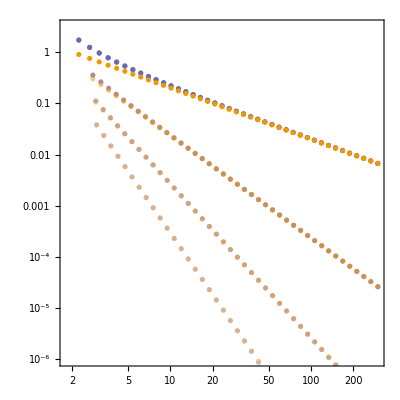

```mathematica
Show[Table[ListLogLogPlot[Table[{allLensingAngles[[a,;;,1]],allLensingAngles[[a,;;,s]]}ᵀ,{s,{2,3,4}}],Joined->False,PlotRange->{All,{10^-6,π}}, PlotStyle->Opacity[1/a]],{a,4}],FrameLabel->MaTeX[{"\\text{periapsis }\\rho_p/\\rho_t","\\text{Lensing angle }\\varphi"}],AspectRatio->1]
```

```mathematica
(* to evaluate this commented cell takes quite some time, with the result (√π Gamma[-α] Tan[π α])/Gamma[-1/2-α] *)
(*Clear[ρp,α]
Integrate[(ρ^2-ρp^2 (ρp/ρ)^(2α))/(ρ^2-ρp^2)ρp/(ρ √(ρ^2-ρp^2)),{ρ,ρp,∞},Assumptions->ρp>0&&α>0]*)
```

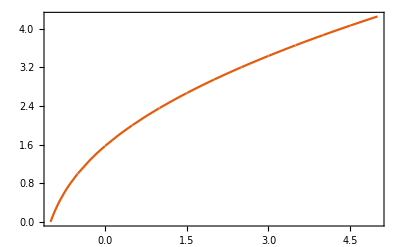

```mathematica
pf=Limit[(√π Gamma[-α] Tan[π α])/Gamma[-(1/2+α)],α->#]&/@αs;
Plot[(√π Gamma[-α] Tan[π α])/Gamma[-(1/2+α)],{α,-1,5},GridLines->{αs,pf},FrameLabel->MaTeX[{"\\alpha","\\sqrt\\pi\\frac{\\Gamma(-\\alpha)\\tan(\\pi\\alpha)}{\\Gamma(-(\\alpha+1/2))}"}]]
```

```mathematica
Clear[α]
(√π Gamma[-α] Tan[π α])/Gamma[-(1/2+α)]/.{Gamma[-α]-> (π Csc[π α])/(α Gamma[α]),Gamma[-(1/2+α)]->  (π Csc[π (1/2+α)])/((1/2+α) Gamma[(1/2+α)])}//FullSimplify
```

(√π Gamma[3/2+α])/Gamma[1+α]

```mathematica
(* export data to CSV file *)
dims=allLensingAngles//Dimensions;
allLensingAnglesMat=ArrayReshape[allLensingAngles,{dims[[1]]*dims[[2]],dims[[3]]}];
αColumn ={Flatten[Table[N[αs[[i]]]*ConstantArray[1,dims[[2]]],{i,Length[αs]}]]}ᵀ;
data=allLensingAnglesMat;
data=Join[αColumn,data,2];
header={"\\alpha","\\rho_p/\\rho_t","\\varphi from trajectories","\\varphi numerical integration","\\varphi approx."};
data=Prepend[data,header];
pathOut=SetDirectory[NotebookDirectory[]];
Export[pathOut<>ToString[StringForm["/lensing_angle_chi_`1`_rhot_`2`_vF_`3`.csv",χ,ρt,vF]],data]
```

/Users/andreashaller/black_hole_mirages/codes/lensing_angle_chi_1_rhot_1_vF_1.csv

Export example trajectory

```mathematica
ti=-20;tf=20;
fun[s_]=solveSEOM[s,Sequence@@x0k0s[[1]],vF,ρt,αs[[1]],χ,ti,tf];
fun[tf]-fun[ti]
makePlots[fun,ρt,αs[[1]],χ,ti,tf,False][[1]]
```

```mathematica
makePlots2D[fun,ρt,αs[[1]],χ,ti,tf,1,2];
```

#### Transverse Shift

```mathematica
Clear[fun,x0,k0,kx0,ky0,t,s,fun,vF,α,χ,ti,tf,ρt,xs,x0k0s]
αs={1/2,1,3/2,2};
χ=+1;ρt=1;vF=1;ti=-10000;tf=-ti;
xs=Table[3*10^x,{x,0,2,0.1}];x0k0s={{#,0,0},1/(√2){0,1,0}}&/@xs;
```

```mathematica
(* this loop takes a minutes on my laptop *)
allTransverseShifts={};
Monitor[
Do[
transverseShifts=transverseShift[#[[1]],#[[2]],vF,ρt,α,χ,ti,tf]&/@x0k0s;
AppendTo[allTransverseShifts,transverseShifts];
,{α,αs}],α]
```

```mathematica
Show[Table[ListLogLogPlot[Table[{allTransverseShifts[[a,;;,2]],-allTransverseShifts[[a,;;,s]]}ᵀ,{s,{3,4,5}}],Joined->False,PlotRange->{All,{10^-6,π}}],{a,Length[αs]}],FrameLabel->MaTeX[{"\\text{periapsis }\\rho_p/\\rho_t","\\text{Transverse shift }\\Delta z"}],AspectRatio->1]
```

```mathematica
(* export data to CSV file *)
dims=allTransverseShifts//Dimensions;
allTransverseShiftsMat=ArrayReshape[allTransverseShifts,{dims[[1]]*dims[[2]],dims[[3]]}];
αColumn ={Flatten[Table[N[αs[[i]]]*ConstantArray[1,dims[[2]]],{i,Length[αs]}]]}ᵀ;

data=allTransverseShiftsMat;
data=Join[αColumn,data,2];
header={"\\alpha", "a","\\rho_p/\\rho_t","\\Delta z from trajectories","\\Delta z numerical integration","\\Delta z approx."};
data=Prepend[data,header];
pathOut=SetDirectory[NotebookDirectory[]];
Export[pathOut<>ToString[StringForm["/transverse_shift_chi_`1`_rhot_`2`_vF_`3`.csv",χ,ρt,vF]],data]
```

```mathematica
ti=-30.23605;tf=100;α=αs[[1]];
transverseShift[Sequence@@x0k0s[[1]],vF,ρt,α,χ,ti,tf]
fun[s_]=solveSEOM[s,Sequence@@x0k0s[[1]],vF,ρt,α,χ,ti,tf];
Show[makePlots2D[fun,ρt,αs[[1]],χ,ti,tf,2,3,False][[1]],Graphics[Arrow[Line[{fun[ti][[1,{2,3}]],fun[tf][[1,{2,3}]]}]]],AspectRatio->1,ImageSize->300]
NMinimize[norm[fun[t][[1,;;2]]],t]
```

```mathematica
fun[0]
```

```mathematica
(* create all necessary data *)
Clear[ts,Nt]
Nt=401;
ts=Range[ti,tf,(tf-ti)/Nt]//N;
If[!MemberQ[ts,0],ts=Sort[AppendTo[ts,0]]];
data={{}};
header={};
(* add parameters *)
data=Join[data,{ts}ᵀ,2];
header=Join[header,{"t"}];
data=Join[data,{α}&/@ts,2];
header=Join[header,{"\\alpha"}];
data=Join[data,{χ}&/@ts,2];
header=Join[header,{"\\chi"}];
data=Join[data,{vF}&/@ts,2];
header=Join[header,{"v_F"}];
data=Join[data,{ρt}&/@ts,2];
header=Join[header,{"\\rho_t"}];
(* add spatial coordinates *)
data=Join[data,fun[#][[1]]&/@ts,2];
header=Join[header,{"x","y", "z"}];
data=Join[data,fun'[#][[1]]&/@ts,2];
header=Join[header,{"\\dot x","\\dot y", "\\dot z"}];
data=Join[data,fun''[#][[1]]&/@ts,2];
header=Join[header,{"\\ddot x","\\ddot y", "\\ddot z"}];
(* add momentum coordinates *)
data=Join[data,fun[#][[2]]&/@ts,2];
header=Join[header,{"k_x","k_y", "k_z"}];
(* spin, angular moment, total angular moment and energy *)
data=Join[data,spin[χ,fun[#][[2]]]&/@ts,2];
header=Join[header,{"s_x","s_y", "s_z"}];
data=Join[data,L[Sequence@@fun[#]]&/@ts,2];
header=Join[header,{"L_x","L_y", "L_z"}];
data=Join[data,J[χ,Sequence@@fun[#]]&/@ts,2];
header=Join[header,{"J_x","J_y", "J_z"}];
data=Join[data,{ϵ[α,vF,ρt,Sequence@@fun[#]]}&/@ts,2];
header=Join[header,{"E"}];
data=Prepend[data,header];
pathOut=SetDirectory[NotebookDirectory[]];
Export[pathOut<>ToString[StringForm["/transverse_shift_example_chi_`1`.csv",χ,ρt,vF]],data]
```

### Lattice Model: Semiclassics linear vs. lattice dispersion

```mathematica
Clear[ϵ,vF]
ϵ[kx_,ky_]=s vF/a √(6-4Cos[ky a]+2Cos[kx a](Cos[ky a]-2))
```

(s vF √(6+2 Cos[a kx] (-2+Cos[a ky])-4 Cos[a ky]))/a

```mathematica
(* series expansion up to second order *)
Clear[x0,vF]
Series[ϵ[(kx-κx)t+κx,(ky-κy)t+κy],{t,0,1}];
Normal[%]/.t->1//ExpandAll//FullSimplify;
Collect[%,{kx,ky}]
```

(kx s vF (2 a Sin[a κx]-a Cos[a κy] Sin[a κx]))/(a √(6+2 Cos[a κx] (-2+Cos[a κy])-4 Cos[a κy]))-(ky s vF (-2+Cos[a κx]) Sin[a κy])/(√(6+2 Cos[a κx] (-2+Cos[a κy])-4 Cos[a κy]))+(s vF (6-4 Cos[a κx]-4 Cos[a κy]+2 Cos[a κx] Cos[a κy]-2 a κx Sin[a κx]+a κx Cos[a κy] Sin[a κx]+a κy (-2+Cos[a κx]) Sin[a κy]))/(a √(6+2 Cos[a κx] (-2+Cos[a κy])-4 Cos[a κy]))

```mathematica
veff[κx_,κy_]=-vF^2/(a ϵ[κx,κy])(Sin[κx a](Cos[κy a]- 2){1,0}+Sin[κy a](Cos[κx a]- 2){0,1})
```

{-(vF (-2+Cos[a κy]) Sin[a κx])/(s √(6+2 Cos[a κx] (-2+Cos[a κy])-4 Cos[a κy])),-(vF (-2+Cos[a κx]) Sin[a κy])/(s √(6+2 Cos[a κx] (-2+Cos[a κy])-4 Cos[a κy]))}

```mathematica
((-veff[κx,κy].{kx,ky}+(kx s vF (2 a Sin[a κx]-a Cos[a κy] Sin[a κx]))/(a √(6+2 Cos[a κx] (-2+Cos[a κy])-4 Cos[a κy]))-(ky s vF (-2+Cos[a κx]) Sin[a κy])/(√(6+2 Cos[a κx] (-2+Cos[a κy])-4 Cos[a κy])))//Simplify)/.{s^2->1}//Simplify
```

0

```mathematica
vp=StreamPlot[Evaluate@veff[κx,κy]/.{vF->1,a->1,s->1},{κx,-π,π},{κy,-π,π},PlotTheme->"Scientific",PlotRangePadding->0,Axes->None,ColorFunction->GrayLevel,StreamMarkers->"Dart",StreamPoints->800];
cp=ContourPlot[Evaluate@(norm[veff[κx,κy]]/.{vF->1,a->1,s->1}),{κx,-π,π},{κy,-π,π},Contours->{0.99,0.9,0.8,0.7},PlotPoints->100,PlotTheme->"Scientific",PlotRangePadding->0,Axes->None,ColorFunction->GrayLevel];
Show[cp,vp,AspectRatio->1/GoldenRatio,FrameStyle->Black,FrameLabel->MaTeX[{"\\kappa_x","\\kappa_y"}]]
```

-Graphics-

```mathematica
Clear[x0,vF]
Normal[Series[veff[kx t,ky t],{t,0,1}]]/.t->1//ExpandAll//FullSimplify
Collect[%.{kx,ky},{κx,κy}]//FullSimplify
```

{(a kx vF)/(√(a^2 (kx^2+ky^2)) s),(a ky vF)/(√(a^2 (kx^2+ky^2)) s)}

(√(a^2 (kx^2+ky^2)) vF)/(a s)

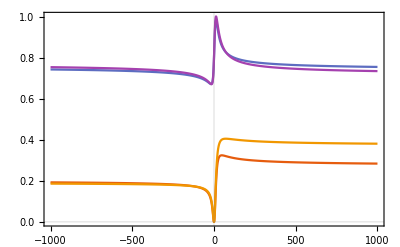

```mathematica
Clear[Ω,χ,v]
(* set Berry curvature to zero here *)
Ω[χ_,v_]:=(0*χ)/2 v/norm[v]^3;

Clear[fun,x0,k0,kx0,ky0,t,s,fun,vF,α,χ,ti,tf,ρt]
(* lattice dispersion *)
Clear[ϵ,α,vF,rt,xs,ks]
ϵ[α_,vF_,rt_,xs_,ks_]:=uv[α,vF,rt,ρ[xs]].Sin[ρ[ks]]+vF*√(6-4Cos[ks[[2]]]+2Cos[ks[[1]]](Cos[ks[[2]]]-2));
vF=1;ρt=1;α=1/2;χ=1;
{x0,k0}={{-10,0,0},{0.0,0.8,0}};
ti=100*x0[[1]];tf=-ti;
(* obtain solution with initial conditions x0, k0 *)
Clear[lensingAnglesLatt]
lensingAnglesLatt[t_]=lensingAngle2[t,x0,k0,vF,ρt,α,χ,ti,tf];
{xi,ki}=lensingAnglesLatt[ti][[4]];
Clear[ϵ]
ϵ[α_,vF_,rt_,xs_,ks_]:=uv[α,vF,rt,ρ[xs]].ρ[ks]+vF*norm[ρ[ks]];
(* obtain solution with initial conditions x0, k0 *)
Clear[lensingAnglesLinApprox]
lensingAnglesLinApprox[t_]=lensingAngle2[t,x0,k0,vF,ρt,α,χ,ti,tf];
Plot[Evaluate@Join[lensingAnglesLatt[t][[4,2,;;2]],lensingAnglesLinApprox[t][[4,2,;;2]]],{t,ti,tf}]
Clear[vFs,vg]
vFs[s_,f_]:=Grad[ϵ[α,vF,0,f[s][[4,1]],{kx,ky,kz}],{kx,ky,kz}]/.{kx->f[s][[4,2,1]],ky->f[s][[4,2,2]],kz->f[s][[4,2,3]]};
vg[s_,f_]:=Grad[ϵ[α,vF,ρt,f[s][[4,1]],{kx,ky,kz}],{kx,ky,kz}]/.{kx->f[s][[4,2,1]],ky->f[s][[4,2,2]],kz->f[s][[4,2,3]]};
```

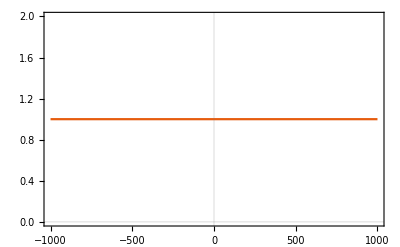

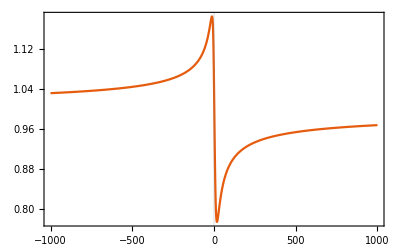

```mathematica
Plot[norm[Evaluate@vFs[t,lensingAnglesLatt]],{t,ti,tf}]
Plot[norm[vg[t,lensingAnglesLatt]],{t,ti,tf}]
```

```mathematica
Clear[Ω,χ,v]
Ω[χ_,v_]:=(0*χ)/2 v/norm[v]^3;

Clear[ks,k0s]
ks={0.01,0.2,0.4,0.6,0.8,1};
k0s = {-#,#,0}&/@ks;
```

```mathematica
deviations={};
trajs={};
Monitor[
Do[
Clear[ϵ,α,vF,rt,xs,ks];
ϵ[α_,vF_,rt_,xs_,ks_]:=uv[α,vF,rt,ρ[xs]].Sin[ρ[ks]]+vF*√(6-4Cos[ks[[2]]]+2Cos[ks[[1]]](Cos[ks[[2]]]-2));
vF=1;ρt=1;α=1/2;χ=1;
xs=Table[3*10^x,{x,0,6,0.2}];
x0s = {-#,0,0}&/@xs;
Clear[lensingAnglesLatt];
lensingAnglesLatt[t_]=lensingAngle2[t,#,k0,vF,ρt,α,χ,ti=-1000000*#[[1]],-ti,False]&/@x0s;
vFeff=norm[Grad[ϵ[α,vF,0,x0s[[1]],{kx,ky,kz}],{kx,ky,kz}]/.{kx->k0[[1]],ky->k0[[2]],kz->k0[[3]]}];
Clear[ϵ,rt,xs,ks];
ϵ[α_,vF_,rt_,xs_,ks_]:=uv[α,1,rt,ρ[xs]].ρ[ks]+vF*norm[ρ[ks]];
lensingAnglesLin=lensingAngle[#,k0,vFeff,ρt,α,χ,ti=-1000000*#[[1]],-ti,False]&/@x0s;
data={{lensingAnglesLin[[;;,1]],lensingAnglesLin[[;;,2]]}ᵀ,{lensingAnglesLatt[t][[;;,2]],lensingAnglesLatt[t][[;;,3]]}ᵀ}ᵀ;
AppendTo[deviations,data];
AppendTo[trajs,lensingAnglesLatt[t][[;;,4]]];
,{k0,k0s}]
,{k0}]
```

```mathematica
xs=Table[3*10^x,{x,0,6,0.2}];
```

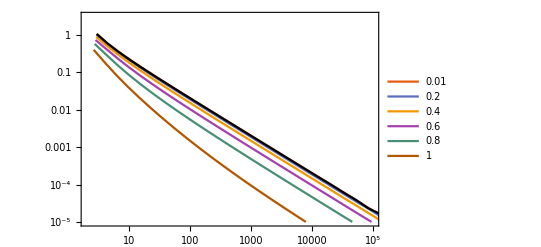

```mathematica
data1=deviations[[1]]ᵀ[[1]];
data2=Table[deviations[[i]]ᵀ[[2]],{i,Length[deviations]}];
data=Join[αColumn,data,2];
linp=ListLogLogPlot[data1,PlotRange->All,Joined->True,PlotStyle->Black];
latp=ListLogLogPlot[data2,PlotRange->{{2,1*^5},{1*^-5,π}},Joined->True,PlotLegends->Placed[k0s[[;;,2]],{Right,Top}]];
Show[latp,linp,FrameLabel->MaTeX[{"\\rho_p/\\rho_t","\\varphi"}]]
```

```mathematica
trajs//Dimensions
```

{6,31,2,3}

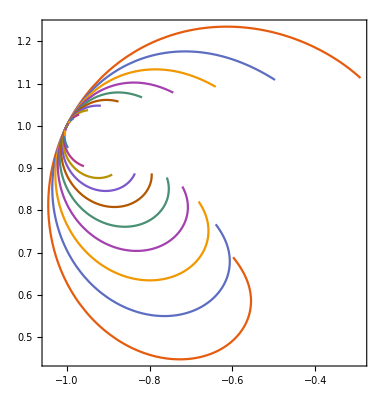

```mathematica
ParametricPlot[Evaluate@trajs[[-1,;;,2,;;2]],{t,-100,100}]
```

### Export example trajectories for python / blender scripts

```mathematica
Clear[fun,x0,k0,kx0,ky0,t,s,fun,vF,α,χ,ti,tf,ρt,data,header1,header2,data1,data2]
vF=1;ρt=1;α=1/2;ti=0;tf=31.5*ρt;
(*{x0,k0}={{0,-20,0},{0.1644,1,0}};*)
{x0,k0}={{0,-20,0}*ρt,{0.167,1,0}/ρt};
(* obtain solution with initial conditions x0, k0 *)
fun[s_]=solveSEOM[s,x0,k0,vF,ρt,α,χ=+1,ti,tf];
Show[makePlots[fun,ρt,α,χ,ti,tf,False][[1]],ViewPoint->{Right}];
makePlots2D[fun,ρt,α,χ,ti,tf,1,2,False][[1]];
{data1,header1}=createData[α,χ,vF,ρt,fun,ti,tf, 201];
fun[s_]=solveSEOM[s,x0,k0,vF,ρt,α,χ=-1,ti,tf];
Show[makePlots[fun,ρt,α,χ,ti,tf,False][[1]],ViewPoint->{Right}];
makePlots2D[fun,ρt,α,χ,ti,tf,1,2,False][[1]];
{data2,header2}=createData[α,χ,vF,ρt,fun,ti,tf, 201];
data=Join[data1,data2];
data=Prepend[data,header1];
pathOut=SetDirectory[NotebookDirectory[]];
Export[pathOut<>ToString[StringForm["/lensing.csv",χ,ρt,vF]],data]
```

```mathematica
Clear[ϵpeff]
ϵpeff[ρ_,Lz_,vF_,α_,ρt_]:=Lz^2/ρ^2(vF^2-u[α,vF,ρt,ρ]^2)
```

```mathematica
ϵpeffs=Table[ϵpeff[norm[ρ[xvs[[i]]]],Lzs[[i]],vF,α,ρt],{i,Length[ts]}];
```

```mathematica
Plot[ϵpeff[norm[ρ[{x,0,0}]],Lzs[[1]],vF,α,ρt],{x,1,10}]
```

```mathematica
Show[DensityPlot[ϵpeff[norm[ρ[{x,y,0}]],Lzs[[1]],vF,α,ρt],{x,-10,10},{y,-10,10},Frame->False,MaxRecursion->15,PlotPoints->100,ClippingStyle->Black,PlotRange->{0,2.5},PlotTheme->"Scientific",PlotRangePadding->0],Graphics[Arrow[Line[xvs[[;;,;;2]]]]],GridLines->None]
```

```mathematica
dtrhosqsLHS=D[norm[ρ[fun[s][[1]]]],s]^2/.{s->#}&/@ts;
dtrhosqsRHS=(ϵs^2-ϵpeffs)/(norm[#]^2&/@kvs);
{dtrhosqsLHS,dtrhosqsRHS}//ListPlot
```

```mathematica
{(D[norm[ρ[fun[s][[1]]]],s]^2/.{s->#}&/@ts)*(norm[#]^2&/@kvs),ϵpeffs,(D[norm[ρ[fun[s][[1]]]],s]^2/.{s->#}&/@ts)*(norm[#]^2&/@kvs)+ϵpeffs}//ListPlot
```

```mathematica
Clear[fun,x0,k0,kx0,ky0,t,s,fun,vF,α,χ,ti,tf,ρt,data,header1,header2,data1,data2]
vF=1;ρt=1;α=1/2;ti=0;tf=30;
ky0 = α/(α+1);
kx0=ky0/(√α);
{x0,k0}={{ρs[ρt,α],0,0},{kx0,ky0,0}/ρt}
```

```mathematica
(* obtain solution with initial conditions x0, k0 *)
fun[s_]=solveSEOM[s,x0,k0,vF,ρt,α,χ=+1,ti,tf];
Show[makePlots[fun,ρt,α,χ,ti,tf,False][[1]],ViewPoint->{Right}];
makePlots2D[fun,ρt,α,χ,ti,tf,1,2,False][[1]];
{data1,header1}=createData[α,χ,vF,ρt,fun,ti,tf, 201];
fun[s_]=solveSEOM[s,x0,k0,vF,ρt,α,χ=-1,ti,tf];
Show[makePlots[fun,ρt,α,χ,ti,tf,False][[1]],ViewPoint->{Right}];
makePlots2D[fun,ρt,α,χ,ti,tf,1,2,False][[1]];
{data2,header2}=createData[α,χ,vF,ρt,fun,ti,tf, 201];
data=Join[data1,data2];
data=Prepend[data,header1];
pathOut=SetDirectory[NotebookDirectory[]];
Export[pathOut<>ToString[StringForm["/unstable_orbit.csv",χ,ρt,vF]],data]
```